```mathematica
ClearAll["Global`*"];
(* Znaleźć wartość przyspieszenia kątowego łopatki turbiny, znajdującej
się w odległości r=800 mm od osi obrotu, po upływie czasu t od
uruchomienia turbiny. Sporządzić wykres dla t=0÷30 s. Zależność
prędkości liniowej łopatki turbiny od czasu wyraża się wzorem: 
v=a·t+b·t.b2,
v=a·t+b·t.b2+c·t.b3, 
gdzie a=1,5 m/s.b2, b=0,5 m/s.b3, c=0,06 m/s⁴. *)

r=0.8;        (* m *)
```

```mathematica
a=1.5;       (* m/s^2 *)
```

```mathematica
b=0.5;        (* m/s^3 *)
```

```mathematica
c=0.06;     (* m/s^4 *)
```

### Wprowadzenie wyrazenia na zaleznosc predkosci liniowej lopatki turbiny ( "v_1" ) od czasu ( "t" ) dla przypadku (a).

```mathematica
v1=a×t+b×t^2;
```

### Obliczenie predkosci katowej ( "ω_1" ) i przyspieszenia katowego ( "ϵ_1" ) dla przypadku (a).

```mathematica
ω1=v1/r;

ϵ1=(∂ω1)/(∂t);
```

### Sporzadzenie wykresu obrazujacego zaleznosc przyspieszenia katowego lopatki turbiny od czasu trwania ruchu dla przypadku (a).

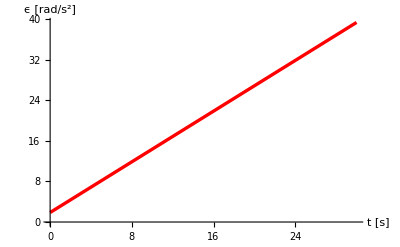

```mathematica
rys1=Plot[ϵ1,{t,0,30},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"t [s] ","ϵ [rad/s^2]"}]
```

### Wprowadzenie wyrazenia na zaleznosc predkosci liniowej lopatki turbiny ( "v_2" ) od czasu ( "t" ) dla przypadku (b).

```mathematica
v2=a×t+b×t^2+c×t^3;
```

### Obliczenie predkosci katowej ( "ω_2" ) i przyspieszenia katowego ( "ϵ_2" ) dla przypadku (b).

```mathematica
ω2=v2/r;

ϵ2=(∂ω2)/(∂t);
```

### Sporzadzenie wykresu obrazujacego zaleznosc przyspieszenia katowego lopatki turbiny od czasu trwania ruchu dla przypadku (b).

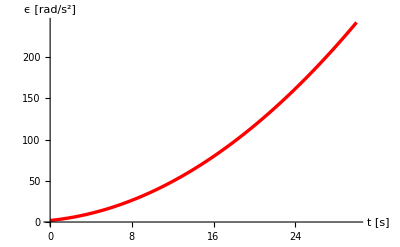

```mathematica
rys1=Plot[ϵ2,{t,0,30},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"t [s] ","ϵ [rad/s^2]"}]
```